```mathematica
Manipulate[
 m
,
Control@Button[Graphics[Rectangle[]],Print[m=4];],
Button[Graphics[Rectangle[]],Print[m=5];]
]
```

```mathematica
Overlay[{Graphics[Disk[]],Graphics[{Red,Disk[]}],Button[x,]}]
```

```mathematica
Button[Graphics[Rectangle[]],Print[4]]
```

```mathematica
Manipulate[
ArrayPlot[rowSweep[5,5]],

]
```

ArrayPlot::mat: Argument rowSweep[5,5] at position 1 is not a list of lists.

Part::partd: Part specification ar⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification ar⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification ar⟦1,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ArrayPlot::mat: Argument rowSweep[5,5] at position 1 is not a list of lists.

```mathematica
color[r_,c_]:=If[ar[[r,c]],1,0];
row[r_,len_]:=Table[color[r,c],{c,len}];
rowSweep[c_,len_]:=Table[row[r,len],{r,c}]
```

```mathematica
row[5,5]
```

{1,0,0,1,1}

```mathematica
rowSweep[5,5]
```

{{1,1,1,1,0},{0,0,0,0,0},{0,0,0,1,1},{1,0,0,0,0},{1,0,0,1,1}}

```mathematica
row[1]
```

{1,1,1,1,0}

```mathematica
color[r_,c_]:=If[ar[[r,c]],1,0]
```

```mathematica
ar = RandomChoice[{True,False},{5,5}]
```

{{True,True,True,True,False},{False,False,False,False,False},{False,False,False,True,True},{True,False,False,False,False},{True,False,False,True,True}}

```mathematica
Column[{
Row[{Button[Dynamic@ArrayPlot[{{x}}],x = Abs[x-1]],DynamicModule[{col=Black},EventHandler[Dynamic[Graphics[{col,Rectangle[]}]],{"MouseDown":>{(col=col/.{White->Black,Black->White}),x = Abs[x-1]}}]]}],
Row[{Dynamic@a,"              ",Dynamic@x}]
}]
```

```mathematica
DynamicModule[{col=White},EventHandler[Dynamic[Graphics[{col,Rectangle[]}]],{"MouseDown":>{(col=col/.{White->Black,Black->White}),x = Abs[x-1]}}]]
```

```mathematica
Dynamic[x]
```

```mathematica
DynamicModule[{a=1},EventHandler[Dynamic@ArrayPlot[{{a}}],{"MouseClicked":>a = Abs[a-1]}]]
```

Set::write: Tag RuleDelayed in MouseClicked:>a$12918 is Protected.

```mathematica
a =1
```

1

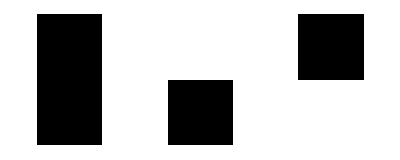

```mathematica
ArrayPlot[{{1,0,0,0,1},{1,0,1}}]
```

```mathematica
Dynamic@ArrayPlot[{{1,0},{Button[],1}}]
```

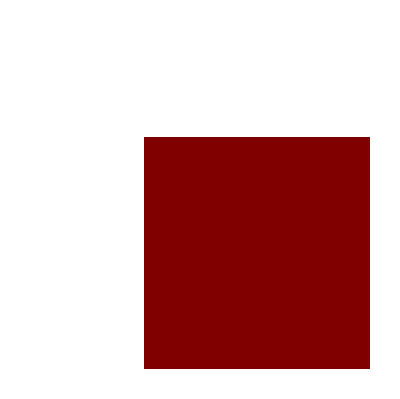

```mathematica
toggle[]:=Button["a",x = Abs[x-1]]
```

```mathematica
x = 1
```

1

```mathematica
Dynamic[x]
```